```mathematica
A=440;
```

```mathematica
Py=Table[2^(n/12), {n,1,12}]
```

{2^(1/12),2^(1/6),2^(1/4),2^(1/3),2^(5/12),√2,2^(7/12),2^(2/3),2^(3/4),2^(5/6),2^(11/12),2}

```mathematica
f[a_]:=Piecewise[{{a,a<2},{a/2,a≥2},{a/4, a≥4}}]
```

```mathematica
Py8=Table[1.0*Py[[i]]*Py[[8]], {i, 1,12}];
Py8=Map[f , Py8];
Py8=Sort[Py8]

F[a_]:=Sort[Map[f, Table[Py[[i]]*Py[[a]],{i,1,12}]]];
```

{1.,1.05946,1.12246,1.18921,1.25992,1.33484,1.41421,1.49831,1.5874,1.68179,1.7818,1.88775}

```mathematica
1.0*F[7]
```

{1.,1.05946,1.12246,1.18921,1.25992,1.33484,1.41421,1.49831,1.5874,1.68179,1.7818,1.88775}

```mathematica
M=Table[1.0*F[i], {i,1,12}];
MatrixForm[%]
```

(1. | 1.05946 | 1.12246 | 1.18921 | 1.25992 | 1.33484 | 1.41421 | 1.49831 | 1.5874 | 1.68179 | 1.7818 | 1.88775
1. | 1.05946 | 1.12246 | 1.18921 | 1.25992 | 1.33484 | 1.41421 | 1.49831 | 1.5874 | 1.68179 | 1.7818 | 1.88775
1. | 1.05946 | 1.12246 | 1.18921 | 1.25992 | 1.33484 | 1.41421 | 1.49831 | 1.5874 | 1.68179 | 1.7818 | 1.88775
1. | 1.05946 | 1.12246 | 1.18921 | 1.25992 | 1.33484 | 1.41421 | 1.49831 | 1.5874 | 1.68179 | 1.7818 | 1.88775
1. | 1.05946 | 1.12246 | 1.18921 | 1.25992 | 1.33484 | 1.41421 | 1.49831 | 1.5874 | 1.68179 | 1.7818 | 1.88775
1. | 1.05946 | 1.12246 | 1.18921 | 1.25992 | 1.33484 | 1.41421 | 1.49831 | 1.5874 | 1.68179 | 1.7818 | 1.88775
1. | 1.05946 | 1.12246 | 1.18921 | 1.25992 | 1.33484 | 1.41421 | 1.49831 | 1.5874 | 1.68179 | 1.7818 | 1.88775
1. | 1.05946 | 1.12246 | 1.18921 | 1.25992 | 1.33484 | 1.41421 | 1.49831 | 1.5874 | 1.68179 | 1.7818 | 1.88775
1. | 1.05946 | 1.12246 | 1.18921 | 1.25992 | 1.33484 | 1.41421 | 1.49831 | 1.5874 | 1.68179 | 1.7818 | 1.88775
1. | 1.05946 | 1.12246 | 1.18921 | 1.25992 | 1.33484 | 1.41421 | 1.49831 | 1.5874 | 1.68179 | 1.7818 | 1.88775
1. | 1.05946 | 1.12246 | 1.18921 | 1.25992 | 1.33484 | 1.41421 | 1.49831 | 1.5874 | 1.68179 | 1.7818 | 1.88775
2. | 1.05946 | 1.12246 | 1.18921 | 1.25992 | 1.33484 | 1.41421 | 1.49831 | 1.5874 | 1.68179 | 1.7818 | 1.88775)

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

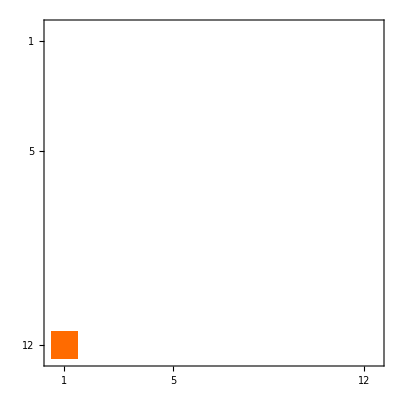

```mathematica
DiffM=Table[1.0*(F[i]-F[1]), {i,1,12}];
MatrixForm[%]
MatrixPlot[%]
```

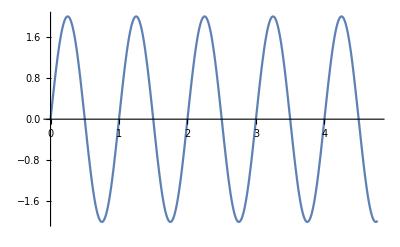
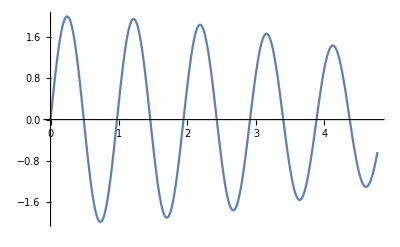
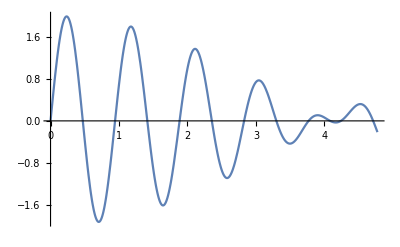
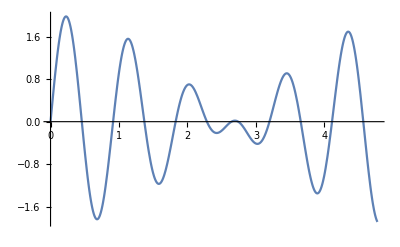
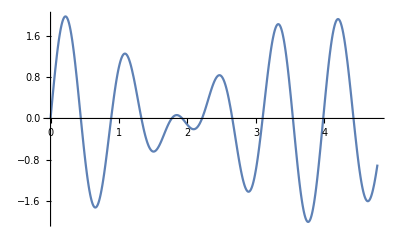
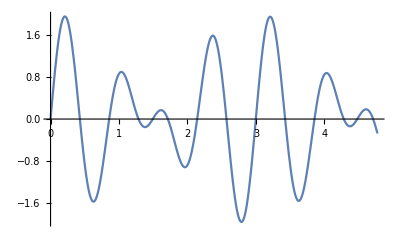
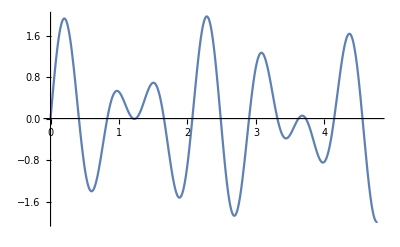
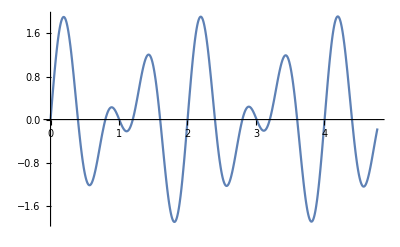

```mathematica
Table[Plot[Sin[F[1][[i]]*2*Pi*t]+Sin[F[1][[1]]*2*Pi*t], {t, 0, 30/(2*Pi)}],{i,1,12}]
```